## README (Introduction)

Motor's RPM is controlled by esc.writeMicroseconds(). By using a linear regression for (us, RPM) data points, we've found a function (fitModel[us]) that models the relation between us and the measured RPM (that is fitModel[us] ~ writeMicroseconds(us)). We've then calculated  by hand it's inverse (inverseFunction[R]) which utilizes the fitted exponential parameter for fitModel. Now, by virtue of being it's inverse, fitModel[inverseFunction[R]] = R and as fitModel approximates writeMicroseconds, we have that writeMicroseconds(inverseFunction(R)) ≈ R, that is, by using inverseFunction we're theoretically able to control the RPM directly.

## Fitting

### Data and input variables

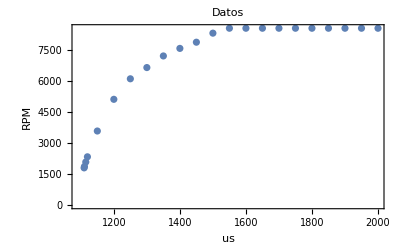

```mathematica
filePath = "C:\\Users\\Lenovo\\Documents\\Laevateinn\\School Projects\\Cuarto semestre\\Taller\\Spincoater\\Data";
fileName = "us_rpm_8V.csv";
fullName = StringJoin[{filePath, "\\", fileName}];
data = Import[fullName, "Data"];
data = data[[2;;]];

ogDataPlot = ListPlot[data, PlotLabel->"Datos", Frame->True, FrameLabel->{"us", "RPM"}, LabelStyle->Directive[FontColor->Black, FontFamily->"Times New Roman", FontSize->15]];

(*Getting starting varibles for model fit.*)
us0 = data[[1, 1]]; (*Starting microseconds.*)
usmax = data[[-1, 1]]; (*End microseconds.*)
Rm = Min[data[[All, 2]]]; (*Minimum rpm*)
RM = Max[data[[All, 2]]]; (*Maximum rpm*)

dataPlot = ListPlot[data, PlotLabel->"Datos", Frame->True, FrameLabel->{"us", "RPM"}, LabelStyle->Directive[FontColor->Black, FontFamily->"Times New Roman", FontSize->15]]
```

### Fitting

1807.23+6764.2 (1-ⅇ^(-k (-1110+u)))

| Estimate | Standard Error | t-Statistic | P-Value
k | 0.00722116 | 0.000150455 | 47.9956 | 5.94495×10^-23

0.00722116

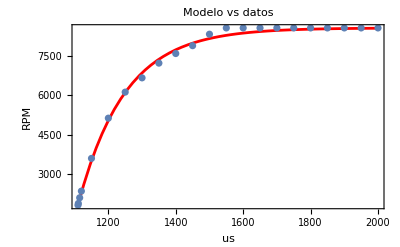

```mathematica
(*As this model takes in us and not real time I'll call the varibles u.*)
unfittedModel = (RM-Rm)(1 - E^(-k (u-us0))) + Rm
fittedModel = NonlinearModelFit[data, unfittedModel, k, u];

(*Fit parameter and standard error.*)
parameterTable = fittedModel["ParameterTable"]
exponentParameter = k/.fittedModel["BestFitParameters"]

fittedModelPlot = Plot[fittedModel[u], {u, us0, usmax}, PlotStyle->Red, PlotLabel->"Modelo", Frame->True,FrameLabel->{"us", "RPM"}, LabelStyle->Directive[FontColor->Black, FontFamily->"Times New Roman", FontSize->15]];
fullPlot = Show[fittedModelPlot, dataPlot, PlotLabel->"Modelo vs datos"]
```

## Linearization

### Linearizing function

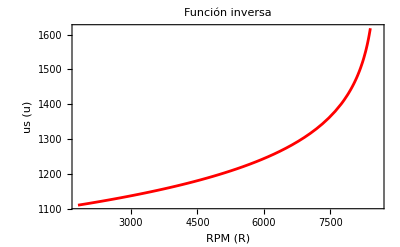

```mathematica
(*Data is linearized when composed with its inverse.*)
(*The inverse of fitModel is a function in terms of RPM (R).*)
inverseFunction[R_] := -Log[1-(R-Rm)/(RM - Rm)]/exponentParameter + us0;

(*Inverse check.*)
identityFunction[R_] := fittedModel[inverseFunction[R]];
identityPlot = Plot[identityFunction[R], {R, 0, 10000}];

(*Minimum and maximum correspond to Rm and RM, the RPM bounds.*)
invserseFunctionPlot = Plot[inverseFunction[R], {R, Rm, RM}, PlotStyle->Red, PlotLabel->"Función inversa", Frame->True,FrameLabel->{"RPM (R)", "us (u)"}, LabelStyle->Directive[FontColor->Black, FontFamily->"Times New Roman", FontSize->15]]
```

### Exporting

```mathematica
exportData = {{"File Name", "ExponentParameter", "MinimumRPM", "MaximumRPM", "MinimumUS", "MaximumUS"}, {fileName, exponentParameter, Rm, RM, us0, usmax}};

currentDate = "13-04-24";
exportFilePath = filePath;
exportName = StringJoin[{currentDate, "_", "parameters_", fileName}];
exportFullName = StringJoin[{exportFilePath, "\\", exportName}];
exportFile = Export[exportFullName, exportData, "CSV", "TextDelimiters"->""]
```

C:\Users\Lenovo\Documents\Laevateinn\School Projects\Cuarto semestre\Taller\Spincoater\Data\13-04-24_parameters_us_rpm_8V.csv